# Test Beckmann vNDF sample

## License

/*
 * Copyright (c) <2023> NVIDIA CORPORATION & AFFILIATES. All rights reserved.
 *
 * Licensed under the Apache License, Version 2.0 (the “License”);
 * you may not use this file except in compliance with the License.
 * You may obtain a copy of the License at
 *
 *     http://www.apache.org/licenses/LICENSE-2.0
 *
 * Unless required by applicable law or agreed to in writing, software
 * distributed under the License is distributed on an “AS IS” BASIS,
 * WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
 * See the License for the specific language governing permissions and
 * limitations under the License.
 */

```mathematica
Run["clang++ -I include test/NDFs/test_beckmann_vNDF.cpp -O3 -o test/NDFs/test_beckmann_vNDF"]
```

0

```mathematica
roughx="0.6";
roughy="1.6";
thetai="2.1";
phi="0.2";
```

```mathematica
argstr=roughx<>" "<>roughy<>" "<>thetai<>" "<>phi<>" 1000000 100 > test/NDFs/MC.txt"
```

0.6 1.6 2.1 0.2 1000000 100 > test/NDFs/MC.txt

```mathematica
Run["./test/NDFs/test_beckmann_vNDF "<>argstr]
```

0

```mathematica
check=Import["test/NDFs/MC.txt","Table"];
```

```mathematica
imEval=check[[-100;;-1]];
imSample=check[[2;;101]];
```

```mathematica
b=.5/Max[Flatten[imSample]];
gamma=0.3;
```

```mathematica
{Image[(b Abs[imEval])^gamma],Image[(b imSample)^gamma],(Image[(b Abs[imEval-imSample])^gamma])}
```

{-Graphics-,-Graphics-,-Graphics-}

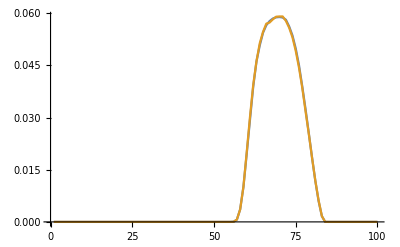

```mathematica
ListPlot[Total/@{Transpose[imEval],Transpose[imSample]},Joined->True,PlotRange->All]
```

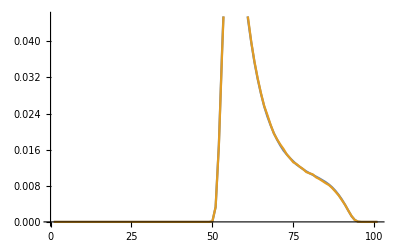

```mathematica
ListPlot[Total/@{imEval,imSample},Joined->True]
```